```mathematica
ABMInputs1600=Import["/Users/thorsilver/Downloads/ABM outputs1/LPtau1600runs_GEMSA_inputs.csv"];

ABMOutputs1600=Import["/Users/thorsilver/Downloads/ABM outputs1/LPtau1600runs GEMSA outputs.csv"];
```

```mathematica
ABMOutputs1600=Function[x,x/1000]/@ABMOutputs1600;
ABMAssoc1600 = AssociationThread[ABMInputs1600 -> Flatten[ABMOutputs1600]];
ABMnewData1600=Dataset[ABMAssoc1600];
ABMNormal1600=Normal[ABMAssoc1600];
ABMNormalRandom=RandomSample[ABMNormal1600];
ABMtrain1600=TakeDrop[ABMNormal1600,1280];
ABMtest1600=ABMtrain1600[[2]];
ABMtraining1600=ABMtrain1600[[1]];
trainDevSplit1600=TakeDrop[ABMtraining1600,1024];
finalTrain1600=trainDevSplit1600[[1]];
finalDev1600=trainDevSplit1600[[2]];
finaltest1600=ABMtest1600;
```

```mathematica
Length[finalDev1600]
Length[finalTrain1600]
Length[finaltest1600]
```

256

1024

320

```mathematica
pRFv1600=Predict[finalTrain1600,Method->"RandomForest"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 1.69 ± 0.082
Method | RandomForest
Single evaluation time | 3.47 ms/example
Batch evaluation speed | 44. examples/ms
Loss | 1.88 ± 0.042
Model memory | 293. kB
Training examples used | 1024 examples
Training time | 666. ms
 |

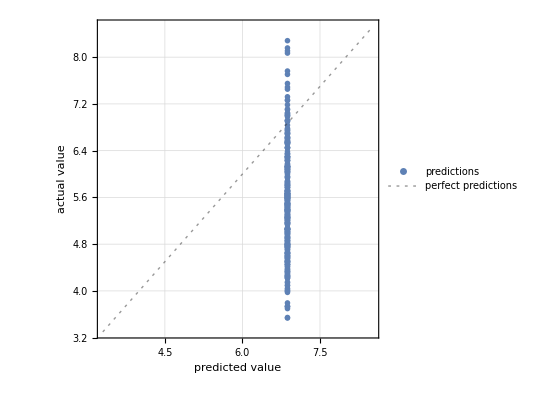

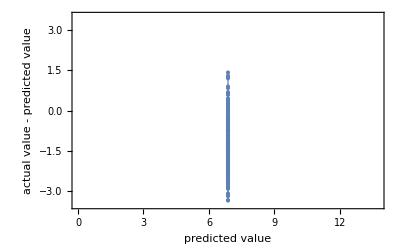

```mathematica
pmRFv1600=PredictorMeasurements[pRFv1600,finaltest1600]
PredictorInformation[pRFv1600]
pmRFv1600["ComparisonPlot"]
pmRFv1600["ResidualPlot"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 1.18 ± 0.37
Method | GradientBoostedTrees
Single evaluation time | 3.62 ms/example
Batch evaluation speed | 49. examples/ms
Loss | 6.01 ± 1.4
Model memory | 451. kB
Training examples used | 1024 examples
Training time | 2.57 s
 |

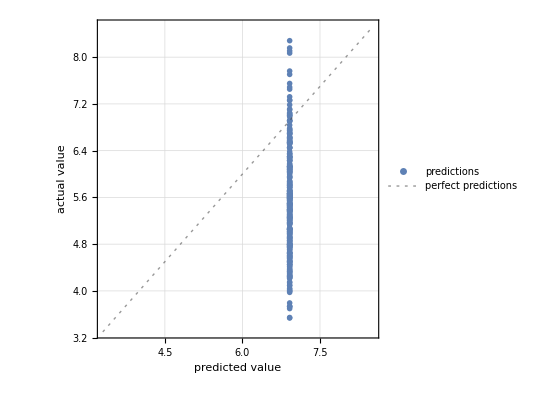

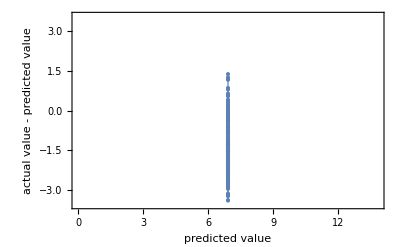

```mathematica
pXGTv1600=Predict[finalTrain1600,Method->"GradientBoostedTrees"]
pmXGTv1600=PredictorMeasurements[pXGTv1600,finaltest1600]
PredictorInformation[pXGTv1600]
pmXGTv1600["ComparisonPlot"]
pmXGTv1600["ResidualPlot"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

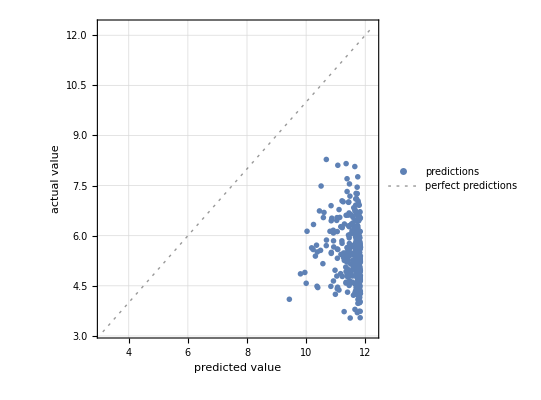

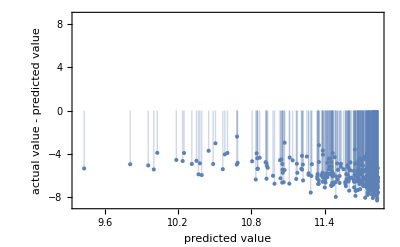

```mathematica
pGPEv1600=Predict[finalTrain1600,Method->"GaussianProcess"]
pmGPEv1600=PredictorMeasurements[pGPEv1600,finaltest1600]
pmGPEv1600["ComparisonPlot"]
pmGPEv1600["ResidualPlot"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 2.11 ± 0.11
Method | DecisionTree
Single evaluation time | 1.4 ms/example
Batch evaluation speed | 384. examples/ms
Loss | 2.18 ± 0.072
Model memory | 153. kB
Training examples used | 1024 examples
Training time | 487. ms
 |

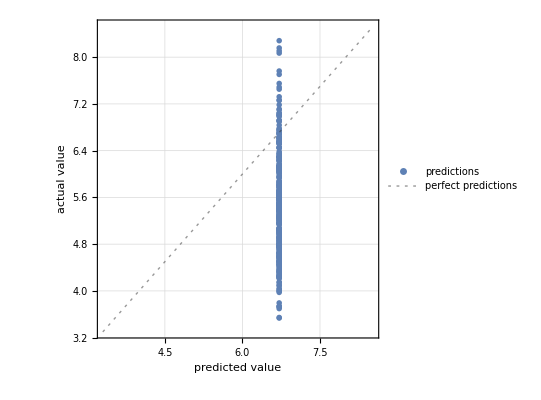

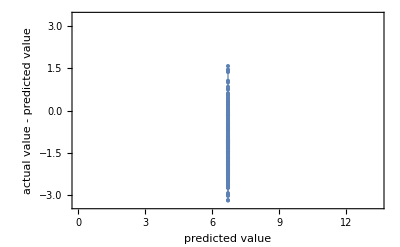

```mathematica
pDTv1600=Predict[finalTrain1600,Method->"DecisionTree"]
pmDTv1600=PredictorMeasurements[pDTv1600,finaltest1600]
PredictorInformation[pDTv1600]
pmDTv1600["ComparisonPlot"]
pmDTv1600["ResidualPlot"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 1.83 ± 0.25
Method | NearestNeighbors
Single evaluation time | 1.5 ms/example
Batch evaluation speed | 99. examples/ms
Loss | 2.11 ± 0.12
Model memory | 218. kB
Training examples used | 1024 examples
Training time | 500. ms
 |

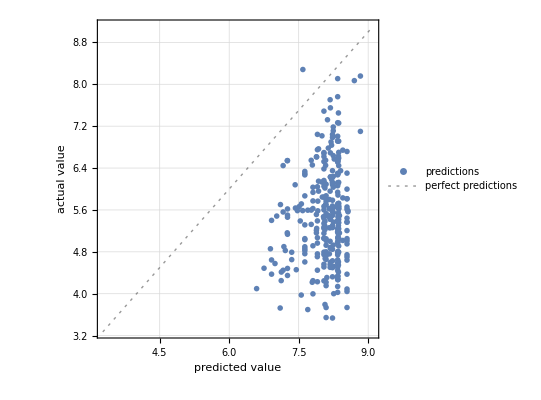

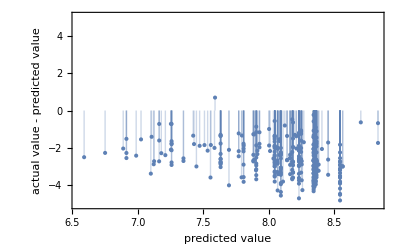

```mathematica
pNearestv1600=Predict[finalTrain1600,Method->"NearestNeighbors"]
pmNearestv1600=PredictorMeasurements[pNearestv1600,finaltest1600]
PredictorInformation[pNearestv1600]
pmNearestv1600["ComparisonPlot"]
pmNearestv1600["ResidualPlot"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 1.58 ± 0.11
Method | LinearRegression
Single evaluation time | 1.61 ms/example
Batch evaluation speed | 288. examples/ms
Loss | 1.79 ± 0.055
Model memory | 325. kB
Training examples used | 1024 examples
Training time | 2.02 s
 |

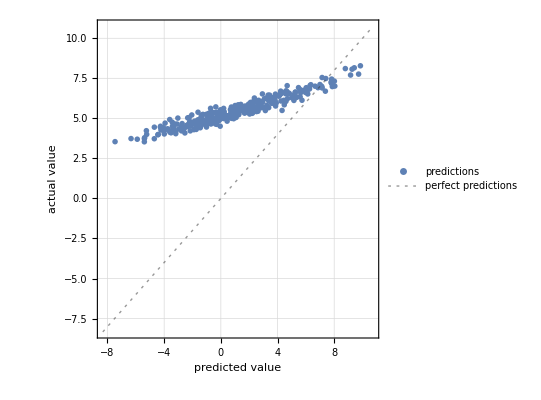

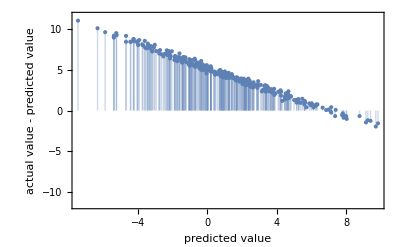

```mathematica
pLRv1600=Predict[finalTrain1600,Method->"LinearRegression"]
pmLRv1600=PredictorMeasurements[pLRv1600,finaltest1600]
PredictorInformation[pLRv1600]
pmLRv1600["ComparisonPlot"]
pmLRv1600["ResidualPlot"]
```

```mathematica
pNNv1600= Predict[finalTrain1600,Method->{"NeuralNetwork", "NetworkDepth"->3,"NetworkType"->"FullyConnected", "L2Regularization"->0.05, MaxTrainingRounds->1000}]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 0.734 ± 0.13
Method | NeuralNetwork
Single evaluation time | 2.13 ms/example
Batch evaluation speed | 49.2 examples/ms
Loss | 0.881 ± 0.082
Model memory | 251. kB
Training examples used | 1024 examples
Training time | 16.3 s
 |

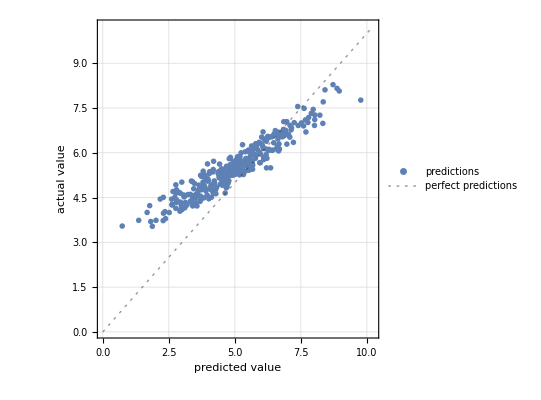

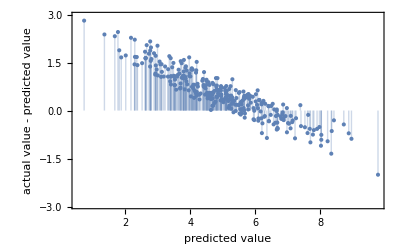

```mathematica
pmNNv1600=PredictorMeasurements[pNNv1600,finaltest1600]
PredictorInformation[pNNv1600]
pmNNv1600["ComparisonPlot"]
pmNNv1600["ResidualPlot"]
```

NetChain[<>]

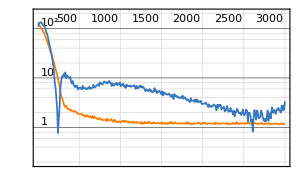
NetTrain Results
summary | ,,  batches:48000  rounds:3000  time:59s  examples/s:52142
data | ,,  training examples:1024  validation examples:320  processed examples:3072000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.22
validation | ,,  loss:4.03
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple1=NetChain[{BatchNormalizationLayer[],Tanh,100,100,100,100,100,100,100,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple1=NetTrain[netSimple1,finalTrain1600,All,ValidationSet->finaltest1600,TargetDevice->"CPU",MaxTrainingRounds->3000,Method->{"ADAM","LearningRate"->0.0001,"L2Regularization"->0.03}]
```

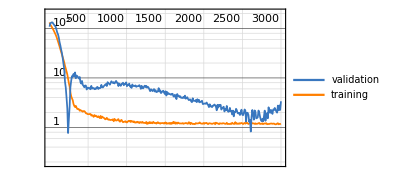
<|Loss→ | rounds
loss | -Graphics-|>

<|Loss→1.22379|>

2606

0.304149

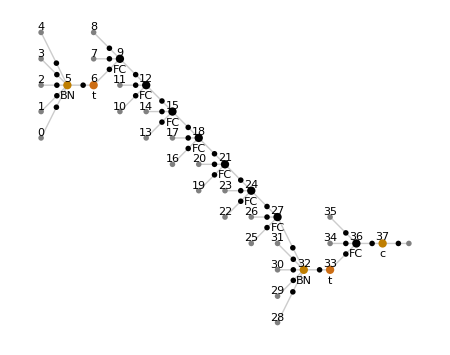

-Graphics-

```mathematica
trainedNetSimple1["FinalPlots"]
trainedNetSimple1["RoundMeasurements"]
best=trainedNetSimple1["BestValidationRound"]
trainedNetSimple1["ValidationLossList"][[best]]
NetInformation[trainedNetSimple1["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple1["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

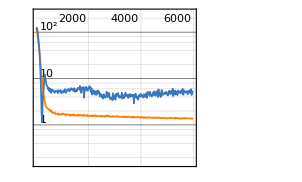
NetTrain Results
summary | ,,  batches:96000  rounds:6000  time:2.9min  examples/s:35130
data | ,,  training examples:1024  validation examples:320  processed examples:6144000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.33
validation | ,,  loss:5.31
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple2=NetChain[{BatchNormalizationLayer[],Tanh,100,100,100,100,100,100,100,100,100,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple2=NetTrain[netSimple2,finalTrain1600,All,ValidationSet->finaltest1600,TargetDevice->"CPU",MaxTrainingRounds->6000,Method->{"ADAM","LearningRate"->0.0001,"L2Regularization"->0.05}]
```

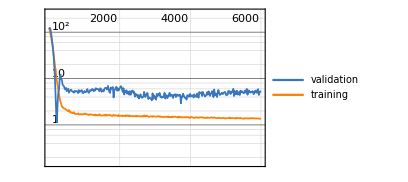
<|Loss→ | rounds
loss | -Graphics-|>

<|Loss→1.32644|>

3167

0.234034

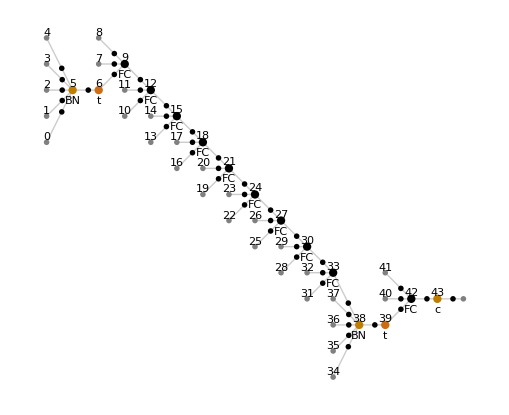

-Graphics-

```mathematica
trainedNetSimple2["FinalPlots"]
trainedNetSimple2["RoundMeasurements"]
best=trainedNetSimple2["BestValidationRound"]
trainedNetSimple2["ValidationLossList"][[best]]
NetInformation[trainedNetSimple2["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple2["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

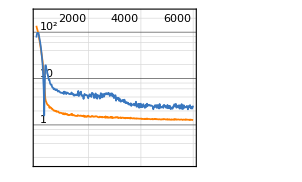
NetTrain Results
summary | ,,  batches:96000  rounds:6000  time:2.0min  examples/s:52104
data | ,,  training examples:1024  validation examples:320  processed examples:6144000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.31
validation | ,,  loss:4.17
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple3=NetChain[{BatchNormalizationLayer[],Tanh,50,50,50,50,50,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple3=NetTrain[netSimple3,finalTrain1600,All,ValidationSet->finaltest1600,TargetDevice->"CPU",MaxTrainingRounds->6000,Method->{"ADAM","LearningRate"->0.0001,"L2Regularization"->0.05}]
```

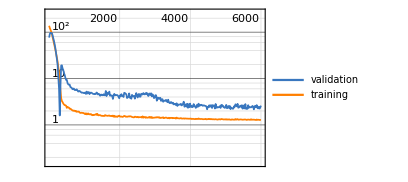
<|Loss→ | rounds
loss | -Graphics-|>

<|Loss→1.31077|>

4527

0.223906

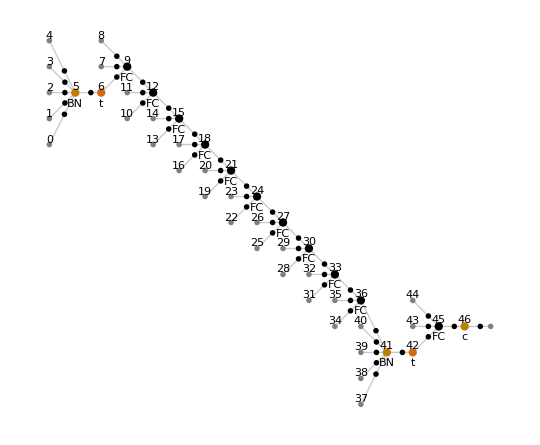

-Graphics-

```mathematica
trainedNetSimple3["FinalPlots"]
trainedNetSimple3["RoundMeasurements"]
best=trainedNetSimple3["BestValidationRound"]
trainedNetSimple3["ValidationLossList"][[best]]
NetInformation[trainedNetSimple3["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple3["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

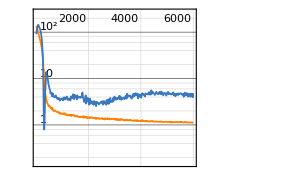
NetTrain Results
summary | ,,  batches:96000  rounds:6000  time:2.2min  examples/s:46989
data | ,,  training examples:1024  validation examples:320  processed examples:6144000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.1
validation | ,,  loss:6.15
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple4=NetChain[{BatchNormalizationLayer[],Tanh,50,50,50,50,50,50,50,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple4=NetTrain[netSimple4,finalTrain1600,All,ValidationSet->finaltest1600,TargetDevice->"CPU",MaxTrainingRounds->6000,Method->{"ADAM","LearningRate"->0.0001,"L2Regularization"->0.05}]
```

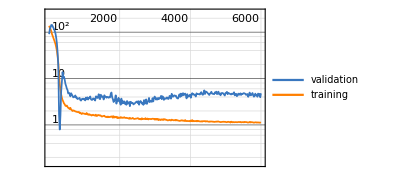
<|Loss→ | rounds
loss | -Graphics-|>

<|Loss→1.09542|>

4094

0.228744

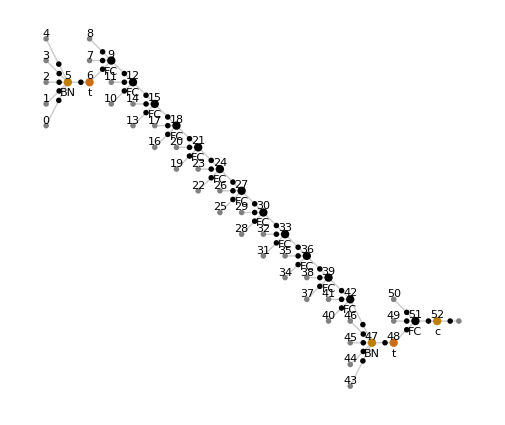

-Graphics-

```mathematica
trainedNetSimple4["FinalPlots"]
trainedNetSimple4["RoundMeasurements"]
best=trainedNetSimple4["BestValidationRound"]
trainedNetSimple4["ValidationLossList"][[best]]
NetInformation[trainedNetSimple4["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple4["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

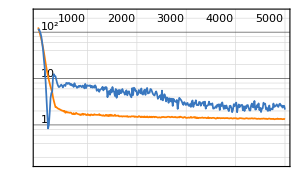
NetTrain Results
summary | ,,  batches:80000  rounds:5000  time:2.5min  examples/s:33834
data | ,,  training examples:1024  validation examples:320  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.31
validation | ,,  loss:2.42
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple5=NetChain[{BatchNormalizationLayer[],Tanh,100,100,100,100,100,100,100,100,100,100,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple5=NetTrain[netSimple5,finalTrain1600,All,ValidationSet->finaltest1600,TargetDevice->"CPU",MaxTrainingRounds->5000,Method->{"ADAM","LearningRate"->0.0001,"L2Regularization"->0.05}]
```

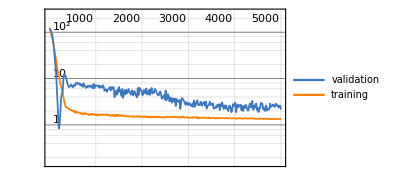
<|Loss→ | rounds
loss | -Graphics-|>

<|Loss→1.30938|>

3872

0.214454

-Graphics-

-Graphics-

```mathematica
trainedNetSimple5["FinalPlots"]
trainedNetSimple5["RoundMeasurements"]
best=trainedNetSimple5["BestValidationRound"]
trainedNetSimple5["ValidationLossList"][[best]]
NetInformation[trainedNetSimple5["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple5["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

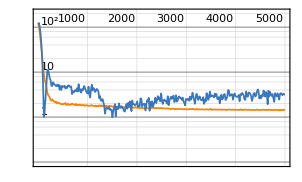
NetTrain Results
summary | ,,  batches:80000  rounds:5000  time:2.1min  examples/s:40876
data | ,,  training examples:1024  validation examples:320  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.41
validation | ,,  loss:6.
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple6=NetChain[{BatchNormalizationLayer[],Tanh,100,100,100,100,100,100,100,100,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple6=NetTrain[netSimple6,finalTrain1600,All,ValidationSet->finaltest1600,TargetDevice->"CPU",MaxTrainingRounds->5000,Method->{"ADAM","LearningRate"->0.0002,"L2Regularization"->0.05}]
```

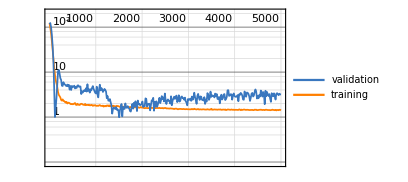
<|Loss→ | rounds
loss | -Graphics-|>

125.258

<|Loss→1.40556|>

2098

0.163367

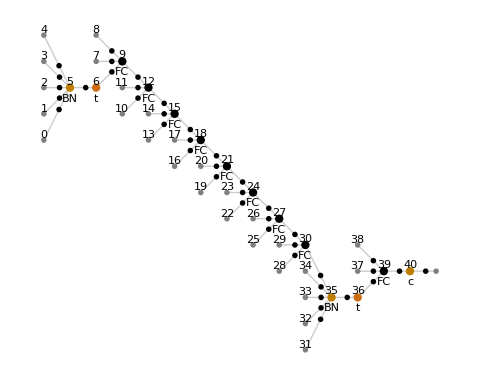

-Graphics-

```mathematica
trainedNetSimple6["FinalPlots"]
trainedNetSimple6["TotalTrainingTime"]
trainedNetSimple6["RoundMeasurements"]
best=trainedNetSimple6["BestValidationRound"]
trainedNetSimple6["ValidationLossList"][[best]]
NetInformation[trainedNetSimple6["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple6["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

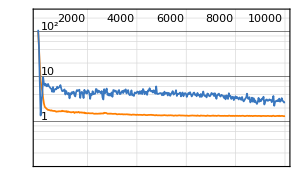
NetTrain Results
summary | ,,  batches:160000  rounds:10000  time:5.0min  examples/s:33806
data | ,,  training examples:1024  validation examples:320  processed examples:10240000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.33
validation | ,,  loss:1.13
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple7=NetChain[{BatchNormalizationLayer[],Tanh,100,100,100,100,100,100,100,100,100,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple7=NetTrain[netSimple7,finalTrain1600,All,ValidationSet->finaltest1600,TargetDevice->"CPU",MaxTrainingRounds->10000,Method->{"ADAM","LearningRate"->0.0002,"L2Regularization"->0.05}]
```

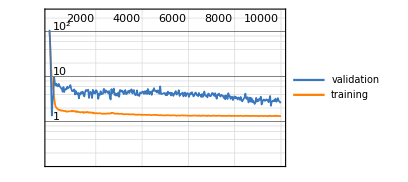
<|Loss→ | rounds
loss | -Graphics-|>

302.904

<|Loss→1.32892|>

2006

0.186545

-Graphics-

-Graphics-

```mathematica
trainedNetSimple7["FinalPlots"]
trainedNetSimple7["TotalTrainingTime"]
trainedNetSimple7["RoundMeasurements"]
best=trainedNetSimple7["BestValidationRound"]
trainedNetSimple7["ValidationLossList"][[best]]
NetInformation[trainedNetSimple7["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple7["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

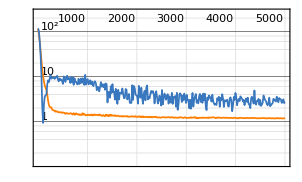
NetTrain Results
summary | ,,  batches:80000  rounds:5000  time:2.4min  examples/s:34955
data | ,,  training examples:1024  validation examples:320  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.15
validation | ,,  loss:7.01
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
net16Simple8=NetChain[{BatchNormalizationLayer[],Tanh,100,100,100,100,100,100,100,100,100,100,BatchNormalizationLayer[],Tanh,1}]
trainedNet16Simple8=NetTrain[net16Simple8,finalTrain1600,All,ValidationSet->finaltest1600,TargetDevice->"CPU",MaxTrainingRounds->5000,Method->{"ADAM","LearningRate"->0.0002,"L2Regularization"->0.03}]
```

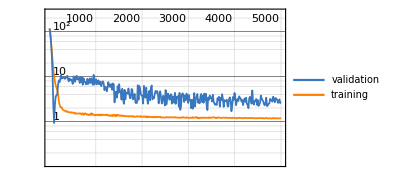
<|Loss→ | rounds
loss | -Graphics-|>

146.474

<|Loss→1.15024|>

2363

0.189905

-Graphics-

-Graphics-

```mathematica
trainedNet16Simple8["FinalPlots"]
trainedNet16Simple8["TotalTrainingTime"]
trainedNet16Simple8["RoundMeasurements"]
best=trainedNet16Simple8["BestValidationRound"]
trainedNet16Simple8["ValidationLossList"][[best]]
NetInformation[trainedNet16Simple8["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNet16Simple8["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

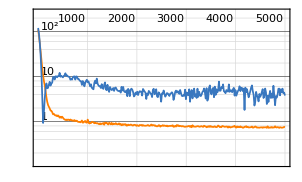
NetTrain Results
summary | ,,  batches:80000  rounds:5000  time:2.7min  examples/s:31984
data | ,,  training examples:1024  validation examples:320  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:7.08×10^-1
validation | ,,  loss:2.07
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
net16Simple9=NetChain[{BatchNormalizationLayer[],Tanh,100,100,100,100,100,100,100,100,100,100,100,BatchNormalizationLayer[],Tanh,1}]
trainedNet16Simple9=NetTrain[net16Simple9,finalTrain1600,All,ValidationSet->finaltest1600,TargetDevice->"CPU",MaxTrainingRounds->5000,Method->{"ADAM","LearningRate"->0.0002,"L2Regularization"->0.01}]
```

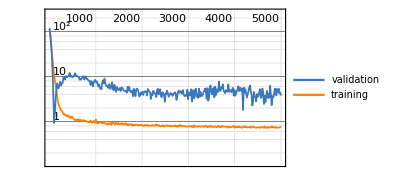
<|Loss→ | rounds
loss | -Graphics-|>

160.082

<|Loss→0.707874|>

4992

0.171547

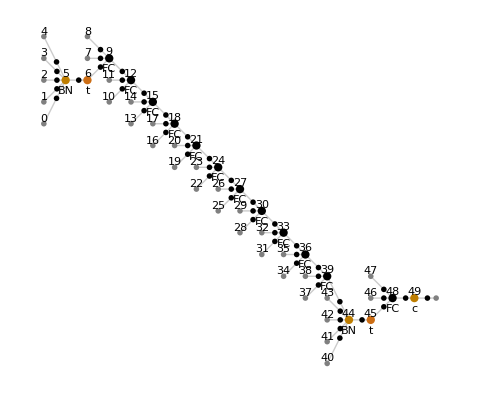

-Graphics-

```mathematica
trainedNet16Simple9["FinalPlots"]
trainedNet16Simple9["TotalTrainingTime"]
trainedNet16Simple9["RoundMeasurements"]
best=trainedNet16Simple9["BestValidationRound"]
trainedNet16Simple9["ValidationLossList"][[best]]
NetInformation[trainedNet16Simple9["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNet16Simple9["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

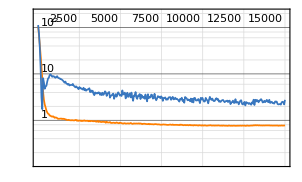
NetTrain Results
summary | ,,  batches:240000  rounds:15000  time:12min  examples/s:22091
data | ,,  training examples:1024  validation examples:320  processed examples:15360000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:7.55×10^-1
validation | ,,  loss:1.48
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
net16Simple10=NetChain[{BatchNormalizationLayer[],Tanh,100,100,100,100,100,100,100,100,100,100,100,BatchNormalizationLayer[],Tanh,1}]
trainedNet16Simple10=NetTrain[net16Simple10,finalTrain1600,All,ValidationSet->finaltest1600,TargetDevice->"CPU",MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.00008,"L2Regularization"->0.02}]
```

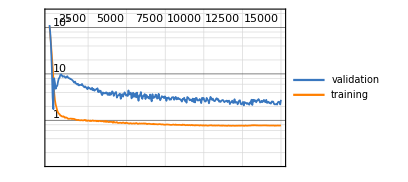
<|Loss→ | rounds
loss | -Graphics-|>

695.307

<|Loss→0.755217|>

12670

0.188035

-Graphics-

-Graphics-

```mathematica
trainedNet16Simple10["FinalPlots"]
trainedNet16Simple10["TotalTrainingTime"]
trainedNet16Simple10["RoundMeasurements"]
best=trainedNet16Simple10["BestValidationRound"]
trainedNet16Simple10["ValidationLossList"][[best]]
NetInformation[trainedNet16Simple10["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNet16Simple10["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

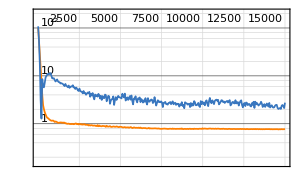
NetTrain Results
summary | ,,  batches:240000  rounds:15000  time:8.8min  examples/s:29132
data | ,,  training examples:1024  validation examples:320  processed examples:15360000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:7.53×10^-1
validation | ,,  loss:1.15
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
net16Simple11=NetChain[{BatchNormalizationLayer[],Tanh,100,100,100,100,100,100,100,100,100,100,100,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNet16Simple11=NetTrain[net16Simple11,finalTrain1600,All,ValidationSet->finaltest1600,TargetDevice->"CPU",MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0001,"L2Regularization"->0.02}]
```

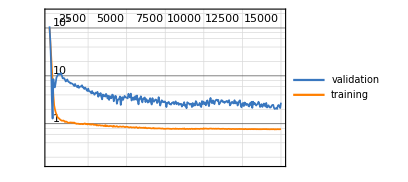
<|Loss→ | rounds
loss | -Graphics-|>

527.261

<|Loss→0.75316|>

5110

0.209511

-Graphics-

-Graphics-

```mathematica
trainedNet16Simple11["FinalPlots"]
trainedNet16Simple11["TotalTrainingTime"]
trainedNet16Simple11["RoundMeasurements"]
best=trainedNet16Simple11["BestValidationRound"]
trainedNet16Simple11["ValidationLossList"][[best]]
NetInformation[trainedNet16Simple11["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNet16Simple11["TrainedNet"],"SummaryGraphic"]
```

### MeanSquare

```mathematica
pmNNv1600["MeanSquare"]
pmDTv1600["MeanSquare"]
pmLRv1600["MeanSquare"]
pmRFv1600["MeanSquare"]
pmXGTv1600["MeanSquare"]
pmGPEv1600["MeanSquare"]
pmLRv1600["MeanSquare"]
pmNearestv1600["MeanSquare"]
```

0.806247

2.24735

24.1802

2.65628

2.77351

37.0196

24.1802

7.40404